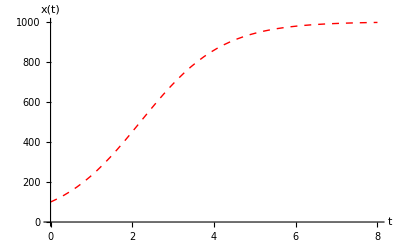

```mathematica
(*Define the differential equation*)
DE=X'[t]==r X[t] (1-X[t]/k);
(*Solve the differential equation with initial condition X[0]==X0*)
soln=DSolve[{DE,X[0]==X0},X[t],t];

(*Substitute parameter values into the solution*)
solnFunc=soln/.{r->1,k->1000,X0->100};

(*Plot the solution*)
Plot[Evaluate[X[t]/.solnFunc],{t,0,8},AxesLabel->{"t","x(t)"},PlotStyle->{Red,Thick,Dashed},AxesStyle->Arrowheads[{0,0.05}]]
```

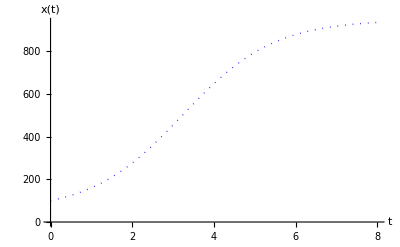

```mathematica
(*Define the differential equation with harvesting*)DE=X'[t]==r X[t] (1-X[t]/k)-h;

(*Solve the differential equation with initial condition X[0]==X0*)
soln=DSolve[{DE,X[0]==X0},X[t],t];

(*Substitute parameter values*)
solnFunc=soln/.{r->1,k->1000,h->50,X0->100};

(*Plot the solution*)
Plot[Evaluate[X[t]/.solnFunc],{t,0,8},AxesLabel->{"t","x(t)"},PlotStyle->{Blue,Thick,Dotted},AxesStyle->Arrowheads[{0,0.05}]]
```